# homework说明文档

张晨晖 asterix314@163.com

## 文件列表

buffer.hpp - 共享队列及常量定义

subscriber.cpp - 订阅者逻辑

publisher.cpp - 发布者逻辑

test.sh - 测试脚本

makefile - 编译脚本

homework.pdf - 说明文档（本文件）

## 设计要点

题目要求进程间通信时延尽量小，因此考虑使用共享内存。publisher和subscriber通过共享内存传输数据，省去了数据拷贝过程，节约时间。

C++的实现中，主要使用了boost.interprocess提供的共享内存支持。在共享内存空间中存放了一些用于同步的信号量和一个队列。两个publisher从队列头部写入数据，一个subscriber从队列尾部取出数据。这些进程互斥地使用队列。subscriber负责创建共享内存。之后就不断试图从队列中取数，队列空则等待。每个publisher每隔1毫秒向队列写入数据，写完规定的数目（2000条）后即退出。subscriber在取出所有的数据（4000条）后，负责销毁共享内存并退出。

为了验证写入的数据最后都被读取出来，publisher向队列写入的数据区域（256字节）的最前面是一个递增的整数。publisher 1 写入0、1、2、……，publisher 2写入2000、2001、2002、……。subscriber将取出的数字排序后就可以验证写入和读取过程都没有出现遗漏。随数据写入的还有当前时间。其与读取时当前时间的差（以纳秒计）即为时延。

程序使用boost.accumulator库提供的统计函数对时延进行分析，计算平均值、标准差等统计量并输出。同时把所有原始时延记录保存为文本文件delays.txt供进一步分析。

## 工具版本及运行结果

编码使用的boost版本1.53.1，编译器为clang++版本3.4，在CentOS 7.3 Linux系统上编译并运行正常。输出样例：

$ ./test.sh
homework test
[S1] starts.
[S1] size of shared buffer set to 4248 bytes.
[S1] created shared buffer 'homework' at 0x6ffffff0000
[S1] receiving messages ...
[P1] starts.
[P1] opened shared buffer 'homework' at 0x6ffffff0000
[P1] sending 1000 messages ...
[P2] starts.
[P2] opened shared buffer 'homework' at 0x6ffffff0000
[P2] sending 1000 messages ...
[P1] exit.
[P2] exit.
[S1] check received messages: ok.
[S1] statistics of delays in nano seconds:
[S1] min = 2285 max = 48247 mean = 4949.57 std = 2785.81
[S1] remove shared buffer and exit.

## 时延分析

程序输出的4000个时延数据导入Mathematica进行绘图。发现时延数据绝大部分集中在2000 - 10000纳秒之间。没有时延进入到2000纳秒以下。

```mathematica
delays=Import["C:\\cygwin64\\home\\zhangchenhui\\work\\vquant-homework\\delay_lock.txt","List"];
```

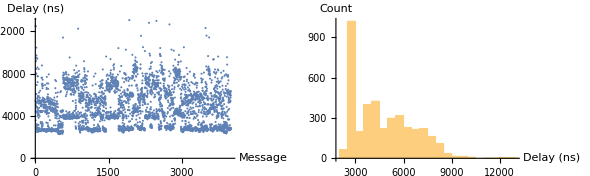

```mathematica
{ListPlot[delays,AxesLabel->{"Message","Delay (ns)"}],
Histogram[delays,AxesLabel->{"Delay (ns)","Count"}]}//GraphicsRow
```

因此2000纳秒应该就是唤醒等待在信号量上的subscriber的时间。这主要是由publisher / subscriber进程切换和同步操作带来的。更长的时延猜测是由来自本系统外的原因导致，比如CPU切换到其他耗时进程、换页、输入输出等。改进的方向应该是尽量将这些外部扰动隔离，比如增加publisher / subscriber的处理器优先级，关闭其他无关进程等等。

## 改进的设计

把微秒计时改为纳秒计时

测试时使用pthread_setaffinity _np或者taskset将publisher和subscriber锁到不同核上

避免publisher和subscriber上的线程切换。我这里提供两个提示：

publisher和subscriber在常态下应该是在busy spin

使用无锁的方式

按照以上三点提示改进设计，前两点比较容易做到。第三点我的理解，关键是subscriber用busy spin的方式不断轮询buffer，发现有新数据写入则马上读取。再结合第2点独占CPU，达到缩小时延的目的。两个publisher是以毫秒的大间隔写入数据，所以不妨仍用互斥锁方式使用buffer。而subscriber不再受此互斥锁限制。

C++实现中，每个buffer的单元分配一个can_write的原子变量（atomic_bool），标示对应单元是否可以写入数据。初始化can_write = true。subscriber用buffer的read()方法读取数据时，不断轮询can_write，等待其变为false（can_read），则马上读取数据。读完数据之后置can_write = true。buffer的write()方法做对应处理。

改进设计后的运行结果如下图。基本上时延降低为改进前的1/10，即绝大部分时延集中在200 - 1000纳秒。没有时延超越200纳秒。考虑到每条消息需要拷贝256字节以及时钟频率~3GHZ，这个相应速度已经比较接近极限了。

```mathematica
delays=Import["C:\\Users\\zhangchenhui\\Documents\\work\\vquant-homework\\delay_busyspin.txt","List"];
```

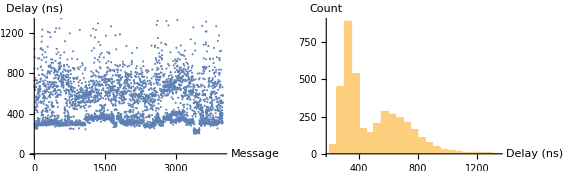

```mathematica
{ListPlot[delays,AxesLabel->{"Message","Delay (ns)"}],
Histogram[delays,AxesLabel->{"Delay (ns)","Count"}]}//GraphicsRow
```